# Sprott #12

```mathematica
TMax=1234;
ySol=NDSolveValue[{
y'''[t]==-0.5y''[t]-y'[t]+y[t]-Sign[y[t]],
y[0]==0,
y'[0]==1,
y''[0]==0}, y,{t,0, TMax}];
Plot[{ySol[t],ySol'[t],ySol''[t]},{t,0, TMax}];
ParametricPlot3D[{ySol[t],ySol'[t],ySol''[t]},{t,0, TMax},
PlotRange->All,
PlotPoints->100]
```

-Graphics3D-

We can write this as a first order system for the vector w=(y
v
a)  where y=y, v=y', and a=v'=y''.
	(y
v
a)'=(y'
v'
a')=(v
a
y''')=(v
a
-0.5 a-v+y -Sign[y])
The cell below defines a function and solve the ODE as the first order system
	w'=f(w)

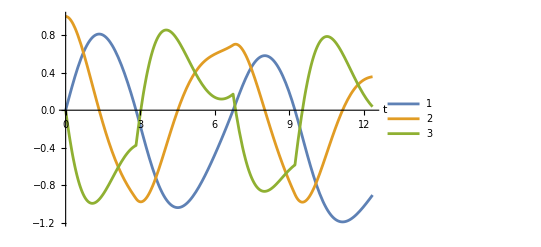

```mathematica
Clear[w]
f[{y_,v_,a_}]:= {v,a, -0.5 a-v+y -Sign[y]}
wSol= NDSolveValue[ {w'[t]==f[w[t]],w[0]=={0,1,0}},w,{t,0,TMax}];
ParametricPlot3D[wSol[t],{t,0, TMax},PlotPoints->100];
Plot[{wSol[t][[1]],wSol[t][[2]],wSol[t][[3]]},{t,0, TMax/100},PlotPoints->100,
PlotLegends->Automatic,
AxesLabel->{"t"," "}]
```